# Análisis de estados promedio bi y tripartitos (último capítulo)

Aquí se harán los cálculos del último capítulo. Para varios estados promedio (generados con el algoritmo MH) se les calculará la pureza, coherencias y entrelazamiento

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"Quantum`"
<<"MaTeX`"
```

SetDelayed::write: Tag PermutationMatrix in PermutationMatrix[p_List] is Protected.

```mathematica
rzs = Table[0.1 i, {i,0,10}];
(*parámetros bipartitos*)
swapPs = Table[0.1 i, {i,0,5}]
```

{0.,0.1,0.2,0.3,0.4,0.5}

```mathematica
rzs = {0, 0.5, 0.8};
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs;
```

## Importando muestras

### Caso de 2 qubits

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples/samples"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples/samples

```mathematica
mhSampleR0Pp3 = Get["MHsample_N=700000_delta=0.05_beta=100_rz=0_p=0.3.wl"][[2,1]];
```

```mathematica
mhSampleR0Pp5 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0_p=0.5.wl"][[2,1]];
```

```mathematica
mhSampleR0Pp8 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0_p=0.8.wl"][[2,1]];
```

```mathematica
Clear[mhSampleR0Pp3, mhSampleR0Pp5, mhSampleR0Pp8]
```

```mathematica
mhSampleRp5Pp3 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0.5_p=0.3.wl"][[2,1]];
```

```mathematica
mhSampleRp5Pp5 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0.5_p=0.5.wl"][[2,1]];
```

```mathematica
mhSampleRp5Pp8 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0.5_p=0.8.wl"][[2,1]];
```

```mathematica
Clear[mhSampleRp5Pp3, mhSampleRp5Pp5, mhSampleRp5Pp8]
```

```mathematica
mhSampleRp8Pp3 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0.8_p=0.3.wl"][[2,1]];
```

```mathematica
mhSampleRp8Pp5 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0.8_p=0.5.wl"][[2,1]];
```

```mathematica
mhSampleRp8Pp8 = Get["MHsample_N=700000_delta=0.03_beta=250_rz=0.8_p=0.8.wl"][[2,1]];
```

```mathematica
Clear[mhSampleRp8Pp3, mhSampleRp8Pp5, mhSampleRp8Pp8]
```

## Estados promedio

### Caso 2 qubits

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples/averages"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples/averages

```mathematica
avgR0Pp3MH = Get["avgs_delta=0.03_beta=250_rz=0_p=0.3_allN.wl"][[1]];
avgR0Pp5MH = Get["avgs_delta=0.03_beta=250_rz=0_p=0.5_allN.wl"][[1]];
avgR0Pp8MH = Get["avgs_delta=0.03_beta=250_rz=0_p=0.8_allN.wl"][[1]];
```

```mathematica
avgRp5Pp3MH = Get["avgs_delta=0.03_beta=250_rz=0.5_p=0.3_allN.wl"][[1]];
avgRp5Pp5MH = Get["avgs_delta=0.03_beta=250_rz=0.5_p=0.5_allN.wl"][[1]];
avgRp5Pp8MH = Get["avgs_delta=0.03_beta=250_rz=0.5_p=0.8_allN.wl"][[1]];
```

```mathematica
avgRp8Pp3MH = Get["avgs_delta=0.03_beta=250_rz=0.8_p=0.3_allN.wl"][[1]];
avgRp8Pp5MH = Get["avgs_delta=0.03_beta=250_rz=0.8_p=0.5_allN.wl"][[1]];
avgRp8Pp8MH = Get["avgs_delta=0.03_beta=250_rz=0.8_p=0.8_allN.wl"][[1]];
```

```mathematica
MapThread[fidelity[#1, #2]&, {{avgR0Pp3MH, avgR0Pp5MH, avgR0Pp8MH},{avgR0Pp3BRUTAL, avgR0Pp5BRUTAL, avgR0Pp8BRUTAL}}]
```

{0.979998,0.995265,0.978795}

```mathematica
MapThread[fidelity[#1, #2]&, {{avgRp5Pp3MH, avgRp5Pp5MH, avgRp5Pp8MH}, {avgRp5Pp3BRUTAL, avgRp5Pp5BRUTAL, avgRp5Pp8BRUTAL}}]
```

{0.995996,0.997645,0.988352}

```mathematica
MapThread[fidelity[#1, #2]&, {{avgRp8Pp3MH, avgRp8Pp5MH, avgRp8Pp8MH}, {avgRp8Pp3BRUTAL, avgRp8Pp5BRUTAL, avgRp8Pp8BRUTAL}}]
```

{0.994892,0.99869,0.997441}

```mathematica
(*brutales*)
avgR0Pp3BRUTAL = preimageMean[sampleR0Pp3BRUTAL];
avgR0Pp5BRUTAL = preimageMean[sampleR0Pp5BRUTAL];
avgR0Pp8BRUTAL = preimageMean[sampleR0Pp8BRUTAL];
avgRp5Pp3BRUTAL = preimageMean[sampleRp5Pp3BRUTAL];
avgRp5Pp5BRUTAL = preimageMean[sampleRp5Pp5BRUTAL];
avgRp5Pp8BRUTAL = preimageMean[sampleRp5Pp8BRUTAL];
avgRp8Pp3BRUTAL = preimageMean[sampleRp8Pp3BRUTAL];
avgRp8Pp5BRUTAL = preimageMean[sampleRp8Pp5BRUTAL];
avgRp8Pp8BRUTAL = preimageMean[sampleRp8Pp8BRUTAL];
```

### Caso 3 qubits

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples_3qubits/averages"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples_3qubits/averages

```mathematica
pes1 = {InputForm[1/3], 0.5, 0.9};
rzs = {0}~Join~Table[0.1 i, {i, 9}]~Join~{1};
```

```mathematica
(*Importando los estados*)
avgsPp33allR = Get["avgs_delta=0.05_beta=100_rz="<>ToString[#]<>"_p=pref_0.33_allN.wl"][[1]]& /@ rzs;
avgsPp5allR = Get["avgs_delta=0.05_beta=100_rz="<>ToString[#]<>"_p=pref_0.5_allN.wl"][[1]]& /@ rzs;
avgsPp9allR = Get["avgs_delta=0.05_beta=100_rz="<>ToString[#]<>"_p=pref_0.9_allN.wl"][[1]]& /@ rzs;
```

## Pureza

### Caso 2 qubits

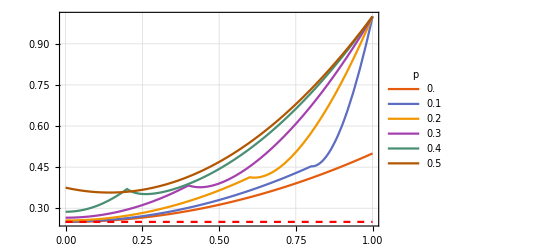

```mathematica
Show[Plot[Evaluate@Table[Purity[ρaverageTwoQubitsbasiscomp[p, r]], {p, swapPs}], {r,0, 1}, 
PlotLegends->LineLegend[swapPs, LegendLabel->"p"], 
PlotTheme->"Scientific", FrameLabel->{MaTeX["r_z", Preamble->{"\\usepackage{newtxmath}"}], MaTeX["\\text{Pu}[\\mathcal{A}[\\varrho_t]]"]}, 
GridLines->Automatic],
Plot[1/4, {x,0,1}, PlotStyle->{Red, Dashed}]]
```

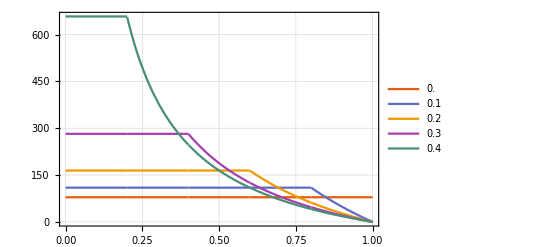

```mathematica
Plot[Evaluate@Table[volBipartiteSubSpaceTarget[p, r], {p, swapPs[[1;;5]]}], {r, 0 ,1}, PlotTheme->"Scientific",
GridLines->Automatic, PlotLegends->swapPs[[1;;5]], PlotRange->All]
```

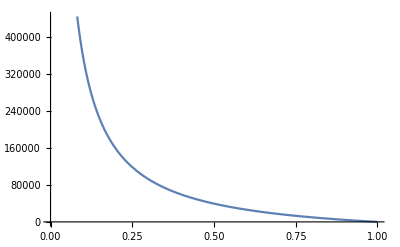

```mathematica
Plot[volBipartiteSubSpaceTarget[0.999, r], {r, 0 ,1}]
```

```mathematica
ρaverageTwoQubitsbasiscomp[0., 0.5]//MatrixForm
```

(0.375 | 0. | 0. | 0.
0. | 0.125 | 0. | 0.
0. | 0. | 0.375 | 0.
0. | 0. | 0. | 0.125)

```mathematica
Export["purity_2qubitsAvg.pdf", %18]
```

purity_2qubitsAvg.pdf

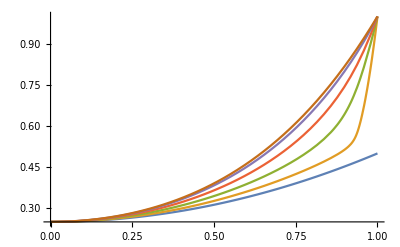

```mathematica
Plot[Evaluate@Table[Purity[MaxEntN[(IdentityMatrix[2] + r*PauliMatrix[3])/2, {p, 1-p}]], {p, swapPs}], {r, 0, 1}, PlotRange->All]
```

### Caso 3 qubits

```mathematica
purities3q = MapThread[{#1, #2}&, {rzs, (Chop@Purity[#]& /@ #)}]& /@ {avgsPp33allR, avgsPp5allR, avgsPp9allR};
```

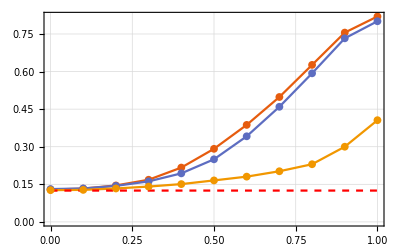

```mathematica
Show[ListPlot[purities3q, PlotTheme->"Scientific", FrameLabel->{MaTeX["r_z", Preamble->{"\\usepackage{newtxmath}"}], MaTeX["\\text{Pu}[\\mathcal{A}[\\varrho_t]]"]},
PlotLegends->LineLegend[MaTeX[pes1], LegendLabel->MaTeX["p_1", Preamble->{"\\usepackage{newtxmath}"}]],
FrameStyle->Black,
Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic],
Plot[1/8, {x, 0, 1}, PlotStyle->{Red, Dashed}]]
```

```mathematica
(*Pruebas*)
target=(IdentityMatrix[2] + PauliMatrix[3])/2;
uinitalState = KroneckerProduct[target,target,target];
```

```mathematica
sampleβ100 = metropolisHastingsSampleNq[5000, 100, 0.01, {0.5, 0.25, 0.25}, uinitalState, target];
fidsβ100 = fidelity[#, KroneckerProduct[target,target,target]]& /@ sampleβ100[[1]];
```

```mathematica
sampleβ500 = metropolisHastingsSampleNq[5000, 500, 0.01, {0.5, 0.25, 0.25}, uinitalState, target];
fidsβ500 = fidelity[#, KroneckerProduct[target,target,target]]& /@ sampleβ500[[1]];
```

```mathematica
sampleβ1000 = metropolisHastingsSampleNq[5000, 1000, 0.01, {0.5, 0.25, 0.25}, uinitalState, target];
fidsβ1000 = fidelity[#, KroneckerProduct[target,target,target]]& /@ sampleβ1000[[1]];
```

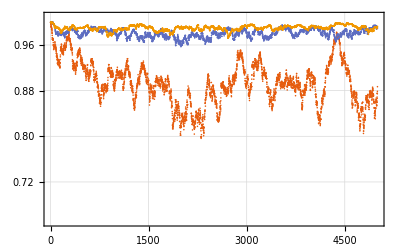

```mathematica
ListPlot[{fidsβ100, fidsβ500, fidsβ1000}, PlotTheme->"Scientific", GridLines->Automatic, PlotRange->{0.65,1.01},
PlotLegends->PointLegend[MaTeX@{100, 500, 1000}, LegendLabel->MaTeX["\\beta", Preamble->{"\\usepackage{newtxmath}"}]],
FrameLabel->MaTeX[{"\\ket{\\psi_i}\\,(i-\\text{ésima iteración})", "F(\\ket{\\psi_i}, \\varrho_t^{\\otimes 3})"}, Preamble->{"\\usepackage{newtxmath, physics}"}],
FrameStyle->Black]
```

```mathematica
Export["fidelities_wrt_pureAvg.pdf", %367]
```

fidelities_wrt_pureAvg.pdf

```mathematica
fidelity[preimageMean[sampleβ100[[1]]], KroneckerProduct[target,target,target]]
fidelity[preimageMean[sampleβ500[[1]]], KroneckerProduct[target,target,target]]
fidelity[preimageMean[sampleβ1000[[1]]], KroneckerProduct[target,target,target]]
```

0.893434

0.980634

0.989742

```mathematica
Chop@Purity[preimageMean[sampleβ100[[1]]]]
Chop@Purity[preimageMean[sampleβ500[[1]]]]
Chop@Purity[preimageMean[sampleβ1000[[1]]]]
```

0.843451

0.963855

0.980102

## Coherencias

```mathematica
coherencesVector[rho_]:= Join @@ Array[rho[[#, # + 1 ;;]]&, Length[rho] - 1];
coherenceMeasure[rho_]:= Norm[coherencesVector[rho]];
```

### Caso 2 qubits

```mathematica
coherence[p_, rz_]:= coherenceMeasure[ρaverageTwoQubitsbasiscomp[p, rz]]
```

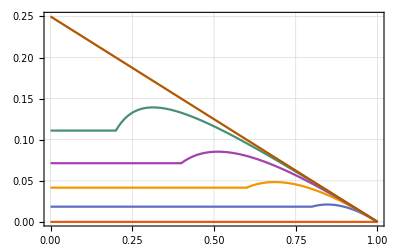

```mathematica
Plot[{coherence[0., r], coherence[0.1, r], coherence[0.2, r], coherence[0.3, r], coherence[0.4, r], coherence[0.5, r]}, {r, 0, 1}, 
PlotLegends->LineLegend[MaTeX[swapPs], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]], 
PlotTheme->"Scientific", FrameLabel->MaTeX[{"r_z", "\\text{Coherencia}\\,\\,(|\\rho_{1,2}|)"}, Preamble->{"\\usepackage{newtxmath}"}],
GridLines->Automatic, FrameStyle->Black]
```

```mathematica
Export["coherence_2qubitsAvg.pdf", %61]
```

coherence_2qubitsAvg.pdf

### Caso 3 qubits

```mathematica
coherences3q = MapThread[{#1, #2}&, {rzs, (coherenceMeasure[#] & /@ #)}]& /@ {avgsPp33allR, avgsPp5allR, avgsPp9allR};
```

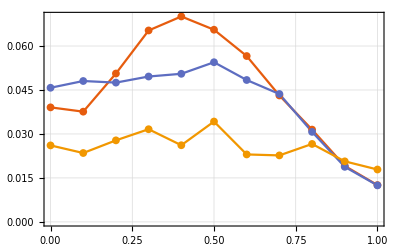

```mathematica
ListPlot[coherences3q, PlotTheme->"Scientific", 
FrameLabel->{MaTeX["r_z", Preamble->{"\\usepackage{newtxmath}"}], MaTeX["\\gamma[\\mathcal{A}[\\varrho_t]]"]},
PlotLegends->LineLegend[MaTeX[pes1], LegendLabel->MaTeX["p_1", Preamble->{"\\usepackage{newtxmath}"}]],
FrameStyle->Black,
Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic]
```

```mathematica
Export["coherence_3qubitAvg.pdf", %34]
```

coherence_3qubitAvg.pdf

```mathematica
(*los "corregidos"*)
coherenceMeasure[preimageMean[sampleβ100[[1]]]]
coherenceMeasure[preimageMean[sampleβ500[[1]]]]
coherenceMeasure[preimageMean[sampleβ1000[[1]]]]
```

0.146703

0.0327559

0.0156774

## Entrelazamiento

### Caso de 2 qubits

```mathematica
(*Concurrencia y entanglement of formation*)
h[x_]:= -x Log[2, x] - (1-x) Log[2, 1-x];
(*h[1]:= 0;*)
entanglementOfFormation[rho_]:= h[(1+Sqrt[1-Concurrence[rho]^2])/2]
```

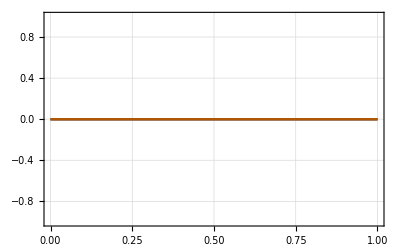

```mathematica
Plot[Evaluate@Table[Concurrence[ρaverageTwoQubitsbasiscomp[p, r]], {p, swapPs}], {r, 0 , 1}, 
PlotTheme->"Scientific", PlotLegends->LineLegend[MaTeX[swapPs], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
FrameLabel->{MaTeX["r_z", Preamble->{"\\usepackage{newtxmath}"}], MaTeX["C[\\mathcal{A}[\\varrho_t]]"]},
FrameStyle->Black, GridLines->Automatic]
```

```mathematica
Export["concurrence_2qubitsAvg.pdf", %223]
```

concurrence_2qubitsAvg.pdf

### Caso de 3 qubits

#### Pruebas

```mathematica
bipartiteNegativity[rho_]:= (traceNorm[PartialTransposeFirst[rho]]-1)/2
```

```mathematica
h[x_]:= -xlog2x[x] - xlog2x[1-x];
eof[rho_]:= h[(1 + Sqrt[1-Concurrence[rho]^2])/2]
```

```mathematica
rho[α_] := α ketsToDensity[{(1/Sqrt[2]) {0,1,-1,0}}][[1]] +  (1-α)(IdentityMatrix[4]/4);
```

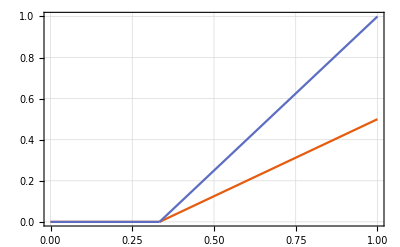

```mathematica
Plot[{bipartiteNegativity[rho[x]], Concurrence[rho[x]]}, {x, 0, 1}, 
PlotLegends->Placed[MaTeX[{"\\text{Negatividad}", "\\text{Concurrencia}"}], {0.3,0.8}], PlotTheme->"Scientific",
FrameLabel->MaTeX[{"\\alpha", "\\text{Valor}"}, Preamble->{"\\usepackage{newtxmath}"}],
GridLines->Automatic, FrameStyle->Black, 
PlotLabel->MaTeX["\\varrho = \\alpha\\dyad{\\Psi^-} + (1-\\alpha)\\mathds{1}/4", Preamble->{"\\usepackage{newtxmath, physics, dsfont}"}]]
```

```mathematica
Export["negativityAndConcurrence_2qubitR0avg.pdf", %98]
```

negativityAndConcurrence_2qubitR0avg.pdf

```mathematica
(*Ahora sí las 6 cantidades para el enlazamiento tripartito (Vidal & Werner)*)
negativity[rho_]:= Abs[Total @ Select[Chop[Eigenvalues[rho]], # < 0 &]];
bisplitNegativities[rho_]:= negativity[PartialTranspose[rho, #]]& /@ Range[3, 1, -1];
residualNegativities[rho_]:= negativity[PartialTransposeFirst@PartialTrace[rho, #]]& /@ {3, 5, 6};
```

```mathematica
rho3q[α_]:= α ketsToDensity[{(1/Sqrt[2]){1,0,0,0,0,0,0,1}}][[1]] + (1-α)(IdentityMatrix[8]/8);
```

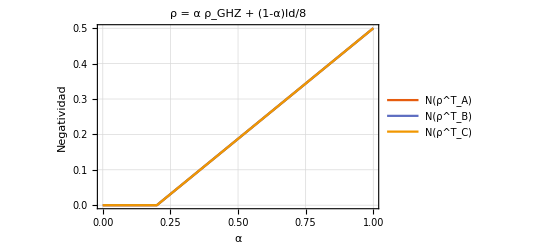
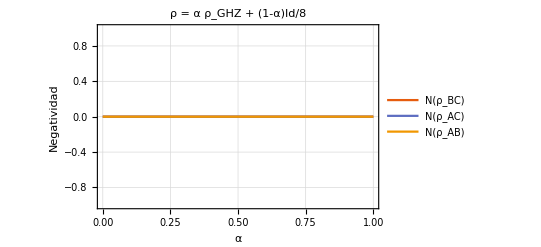
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[{bisplitNegativities[rho3q[α]][[1]], bisplitNegativities[rho3q[α]][[2]], bisplitNegativities[rho3q[α]][[3]]}, {α, 0, 1}, 
PlotTheme->"Scientific", PlotLegends->{"N(ρ^T_A)", "N(ρ^T_B)", "N(ρ^T_C)"}, FrameLabel->{"α", "Negatividad"}, GridLines->Automatic,
PlotLabel->"ρ = α ρ_GHZ + (1-α)Id/8"],
Plot[{residualNegativities[rho3q[α]][[1]], residualNegativities[rho3q[α]][[2]], residualNegativities[rho3q[α]][[3]]}, {α, 0, 1}, 
PlotTheme->"Scientific", PlotLegends->{"N(ρ_BC)", "N(ρ_AC)", "N(ρ_AB)"}, FrameLabel->{"α", "Negatividad"}, GridLines->Automatic,
PlotLabel->"ρ = α ρ_GHZ + (1-α)Id/8"]}
}, ItemStyle->ImageSizeMultipliers->1, Spacings->{1, 1}]
```

```mathematica
(*probando con un estado no máximamente entrelazado*)
rho3qSecond[α_]:= α ketsToDensity[{(1/Sqrt[2]) {0,1,-1,0,0,0,0,0}}][[1]] + (1-α)(IdentityMatrix[8]/8);
```

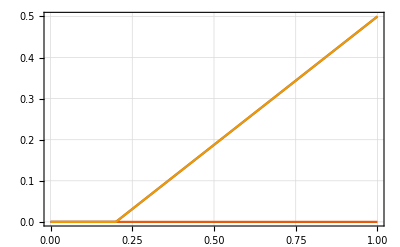

```mathematica
Plot[{bisplitNegativities[rho3qSecond[α]][[1]], bisplitNegativities[rho3qSecond[α]][[2]], bisplitNegativities[rho3qSecond[α]][[3]]}, {α, 0, 1}, 
PlotTheme->"Scientific", PlotLegends->MaTeX[{"N(\\varrho^{T_A})", "N(\\varrho^{T_B})", "N(\\varrho^{T_C})"}, Preamble->{"\\usepackage{newtxmath}"}],
FrameLabel->MaTeX[{"\\alpha", "\\text{Negatividad}"}, Preamble->{"\\usepackage{newtxmath}"}], GridLines->Automatic,
PlotLabel->MaTeX["\\varrho = \\alpha\\dyad{\\psi} + (1-\\alpha)\\mathds{1}/8", Preamble->{"\\usepackage{newtxmath, physics, dsfont}"}],
FrameStyle->Black]
```

```mathematica
Export["bisplitNegativities_compund3qubitState.pdf", %56]
```

bisplitNegativities_compund3qubitState.pdf

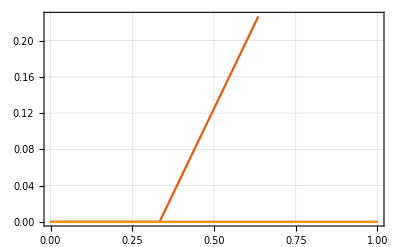

```mathematica
Plot[{residualNegativities[rho3qSecond[α]][[1]], residualNegativities[rho3qSecond[α]][[2]], residualNegativities[rho3qSecond[α]][[3]]}, {α, 0, 1}, 
PlotTheme->"Scientific", PlotLegends->MaTeX[{"N(\\varrho_{BC})", "N(\\varrho_{AC})", "N(\\varrho_{AB})"}, Preamble->{"\\usepackage{newtxmath}"}],
FrameLabel->MaTeX[{"\\alpha", "\\text{Negatividad residual}"}, Preamble->{"\\usepackage{newtxmath}"}], GridLines->Automatic,
PlotLabel->MaTeX["\\varrho = \\alpha\\dyad{\\psi} + (1-\\alpha)\\mathds{1}/8", Preamble->{"\\usepackage{newtxmath, physics, dsfont}"}],
FrameStyle->Black]
```

```mathematica
Export["residualNegativities_compound3qubitState.pdf", %96]
```

residualNegativities_compound3qubitState.pdf

#### Ahora sí, los estados promedio

```mathematica
bisplitNegativitiesData = Transpose[(bisplitNegativities[#]& /@ #)]& /@ {avgsPp33allR, avgsPp5allR, avgsPp9allR};
residualNegativitiesData = Transpose[(residualNegativities[#]& /@ #)]& /@ {avgsPp33allR, avgsPp5allR, avgsPp9allR};
```

```mathematica
dataArrange[data_]:= Map[MapThread[{#1, #2}&, {rzs, #}]&, data];
```

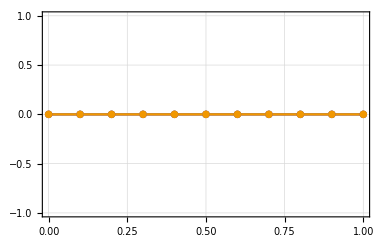
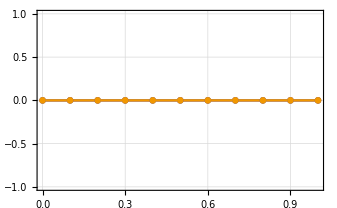

```mathematica
{ListPlot[dataArrange@bisplitNegativitiesData[[1]], PlotTheme->"Scientific",
		 PlotLegends->Placed[MaTeX[{"N(\\mathcal{A}[\\varrho_t]^{T_A})", "N(\\mathcal{A}[\\varrho_t]^{T_B})", "N(\\mathcal{A}[\\varrho_t]^{T_C})"}], {0.84,0.23}],
		 Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, FrameStyle->Black,
		 PlotLabel->MaTeX["p_1 = 1/3", Preamble->{"\\usepackage{newtxmath}"}],
		 FrameLabel->MaTeX[{"r_z", "\\text{Negatividad}"}, Preamble->{"\\usepackage{newtxmath}"}]],
ListPlot[dataArrange@residualNegativitiesData[[1]], PlotTheme->"Scientific",
		 PlotLegends->Placed[MaTeX[{"N(\\mathcal{A}[\\varrho_t]_{BC})", "N(\\mathcal{A}[\\varrho_t]_{AC})", "N(\\mathcal{A}[\\varrho_t]_{AB})"}], {0.84,0.23}],
		 Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, FrameStyle->Black,
		 PlotLabel->MaTeX["p_1 = 1/3", Preamble->{"\\usepackage{newtxmath}"}],
		 FrameLabel->MaTeX[{"r_z", "\\text{Negatividad residual}"}, Preamble->{"\\usepackage{newtxmath}"}]]
}
```

```mathematica
Export["residualNegativities_3qubitsP1=0.33.pdf", %120[[2]]]
```

residualNegativities_3qubitsP1=0.33.pdf

```mathematica
(*los "corregidos"*)
bisplitNegativities[preimageMean[sampleβ100[[1]]]]
bisplitNegativities[preimageMean[sampleβ500[[1]]]]
bisplitNegativities[preimageMean[sampleβ1000[[1]]]]
```

{0.0433327,0.0175811,0.0399162}

{0.00782869,0.00858199,0.00974021}

{0.0046732,0.00592128,0.00405709}

```mathematica
residualNegativities[preimageMean[sampleβ100[[1]]]]
residualNegativities[preimageMean[sampleβ500[[1]]]]
residualNegativities[preimageMean[sampleβ1000[[1]]]]
```

{0,0.0282201,0}

{0.00435069,0.00375435,0.000178779}

{0.00183694,0,0.00226785}

## Gráficas cilíndricas

```mathematica
generalLegend = 
Grid[{{SwatchLegend[{Darker[Red,.2], Darker[Green, .2]}, 
					MaTeX[{"\\tr_A", "\\tr_B"}, Preamble->{"\\usepackage{physics, newtxmath}"}, FontSize->20], 
					LegendLabel->MaTeX["\\text{Metropolis-Hastings}", FontSize->20], 
					LegendLayout->"Row",
					LegendMarkerSize->20]},
	   {SwatchLegend[{Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, 
	                 MaTeX[{"\\tr_A", "\\tr_B"}, Preamble->{"\\usepackage{physics, newtxmath}"}, FontSize->20], 
	                 LegendLabel->MaTeX["\\text{Brutal}", FontSize->20], 
	                 LegendLayout->"Row",
	                 LegendMarkerSize->20]}
}];
```

### Objetivo r_z = 0

#### p = 0.3

```mathematica
sampleR0Pp3BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.m"]];
```

```mathematica
cylPlotsR0Pp3BRUTAL = tripleCylindricalPlotNoFilling[sampleR0Pp3BRUTAL, 0, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {{0,0.2}, {0,6.2}, {-0.2,0.2}},
{5, Automatic, 5}];
```

```mathematica
cylPlotsR0Pp3MH= tripleCylindricalPlotNoFilling[mhSampleR0Pp3, 0, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.2}, {0,6.2}, {-0.2,0.2}}];
```

```mathematica
Table[Show[cylPlotsR0Pp3BRUTAL[[i]], cylPlotsR0Pp3MH[[i]]], {i,3}]
```

```mathematica
spherePlotR0Pp3MH = visualizeBipartiteSystem[mhSampleR0Pp3[[200000;;]]];
spherePlotR0Pp3BRUTAL = visualizeBipartiteSystem[sampleR0Pp3BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0,\\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsR0Pp3MH[[i]], cylPlotsR0Pp3BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotR0Pp3MH, spherePlotR0Pp3BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_R0Pp3_beta=100_delta=0.05_N=700000.pdf", %28]
```

mhFinalResults_R0Pp3_beta=100_delta=0.05_N=700000.pdf

#### p = 0.5

```mathematica
sampleR0Pp5BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.m"]];
```

```mathematica
cylPlotsR0Pp5BRUTAL = tripleCylindricalPlotNoFilling[sampleR0Pp5BRUTAL, 0, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
cylPlotsR0Pp5MH = tripleCylindricalPlotNoFilling[mhSampleR0Pp5, 0, {Darker[Red,.2], Darker[Green, .2]}, {Full, {0,6.2}, Full}];
```

```mathematica
Table[Show[cylPlotsR0Pp5BRUTAL[[i]], cylPlotsR0Pp5MH[[i]]], {i,3}]
```

```mathematica
spherePlotR0Pp5MH = visualizeBipartiteSystem[mhSampleR0Pp5[[350000;;]]];
spherePlotR0Pp5BRUTAL = visualizeBipartiteSystem[sampleR0Pp5BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0,\\, p = 0.5", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsR0Pp5MH[[i]], cylPlotsR0Pp5BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotR0Pp5MH, spherePlotR0Pp5BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_R0Pp5_beta=250_delta=0.03_N=700000.pdf", %45]
```

mhFinalResults_R0Pp5_beta=250_delta=0.03_N=700000.pdf

#### p = 0.8

```mathematica
sampleR0Pp8BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.m"]];
```

```mathematica
cylPlotsR0Pp8BRUTAL = tripleCylindricalPlotNoFilling[sampleR0Pp8BRUTAL, 0, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {{0,0.08}, {0,6.2}, {-0.06,0.06}},
{10, Automatic, 10}];
```

```mathematica
cylPlotsR0Pp8MH = tripleCylindricalPlotNoFilling[mhSampleR0Pp8, 0, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.08}, {0,6.2}, {-0.06,0.06}}];
```

```mathematica
Table[Show[cylPlotsR0Pp8BRUTAL[[i]], cylPlotsR0Pp8MH[[i]]], {i,3}]
```

```mathematica
spherePlotR0Pp8MH = visualizeBipartiteSystem[mhSampleR0Pp8[[400000;;]]];
spherePlotR0Pp8BRUTAL = visualizeBipartiteSystem[sampleR0Pp8BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0,\\, p = 0.8", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsR0Pp8MH[[i]], cylPlotsR0Pp8BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotR0Pp8MH, spherePlotR0Pp8BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_R0Pp8_beta=250_delta=0.03_N=700000.pdf", %25]
```

mhFinalResults_R0Pp8_beta=250_delta=0.03_N=700000.pdf

### Objetivo r_z = 0.5

#### p = 0.3

```mathematica
sampleRp5Pp3BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"]];
```

```mathematica
cylPlotsRp5Pp3BRUTAL = tripleCylindricalPlotNoFilling[sampleRp5Pp3BRUTAL, 0.5, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {{0,0.9}, {0,6.21}, Full}];
```

```mathematica
cylPlotsRp5Pp3MH = tripleCylindricalPlotNoFilling[mhSampleRp5Pp3, 0.5, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.9}, {0,6.2}, Full}, {Automatic, Automatic, 30}];
```

```mathematica
Table[Show[cylPlotsRp5Pp3BRUTAL[[i]], cylPlotsRp5Pp3MH[[i]]], {i,3}]
```

```mathematica
spherePlotRp5Pp3MH = visualizeBipartiteSystem[mhSampleRp5Pp3[[400000;;]]];
spherePlotRp5Pp3BRUTAL = visualizeBipartiteSystem[sampleRp5Pp3BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.5,\\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp5Pp3MH[[i]], cylPlotsRp5Pp3BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp5Pp3MH, spherePlotRp5Pp3BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp5Pp3_beta=250_delta=0.03_N=700000.pdf", %39]
```

mhFinalResults_Rp5Pp3_beta=250_delta=0.03_N=700000.pdf

#### p = 0.5

```mathematica
sampleRp5Pp5BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.5.m"]];
```

```mathematica
cylPlotsRp5Pp5BRUTAL = tripleCylindricalPlotNoFilling[sampleRp5Pp5BRUTAL, 0.5, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {{0,0.85}, {0,6.2}, Full}, {Automatic, Automatic, 10}];
```

```mathematica
cylPlotsRp5Pp5MH = tripleCylindricalPlotNoFilling[mhSampleRp5Pp5, 0.5, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.85}, {0,6.2}, {-0.15, 0.15}}];
```

```mathematica
Table[Show[cylPlotsRp5Pp5BRUTAL[[i]], cylPlotsRp5Pp5MH[[i]]], {i,3}]
```

```mathematica
spherePlotRp5Pp5MH = visualizeBipartiteSystem[mhSampleRp5Pp5[[400000;;]]];
spherePlotRp5Pp5BRUTAL = visualizeBipartiteSystem[sampleRp5Pp5BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.5,\\, p = 0.5", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp5Pp5MH[[i]], cylPlotsRp5Pp5BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp5Pp5MH, spherePlotRp5Pp5BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp5Pp5_beta=250_delta=0.03_N=700000.pdf", %20]
```

mhFinalResults_Rp5Pp5_beta=250_delta=0.03_N=700000.pdf

#### p = 0.8

```mathematica
sampleRp5Pp8BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.5.m"]];
```

```mathematica
cylPlotsRp5Pp8BRUTAL = tripleCylindricalPlotNoFilling[sampleRp5Pp8BRUTAL, 0.5, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}, {20, Automatic, Automatic}];
```

```mathematica
cylPlotsRp5Pp8MH = tripleCylindricalPlotNoFilling[mhSampleRp5Pp8, 0.5, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.7}, {0,6.2}, Full}];
```

```mathematica
Table[Show[cylPlotsRp5Pp8BRUTAL[[i]], cylPlotsRp5Pp8MH[[i]]], {i,3}]
```

```mathematica
spherePlotRp5Pp8MH = visualizeBipartiteSystem[mhSampleRp5Pp8[[400000;;]]];
spherePlotRp5Pp8BRUTAL = visualizeBipartiteSystem[sampleRp5Pp8BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.5,\\, p = 0.8", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp5Pp8MH[[i]], cylPlotsRp5Pp8BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp5Pp8MH, spherePlotRp5Pp8BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp5Pp8_beta=250_delta=0.03_N=700000.pdf", %35]
```

mhFinalResults_Rp5Pp8_beta=250_delta=0.03_N=700000.pdf

### Objetivo r_z = 0.8

#### p = 0.3

```mathematica
sampleRp8Pp3BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.8.m"]];
```

```mathematica
cylPlotsRp8Pp3BRUTAL = tripleCylindricalPlotNoFilling[sampleRp8Pp3BRUTAL, 0.8, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}, {Automatic, Automatic, 20}];
```

```mathematica
cylPlotsRp8Pp3MH = tripleCylindricalPlotNoFilling[mhSampleRp8Pp3, 0.8, {Darker[Red,.2], Darker[Green, .2]}, {Full, {0,6.2}, Full}];
```

```mathematica
Table[Show[cylPlotsRp8Pp3BRUTAL[[i]], cylPlotsRp8Pp3MH[[i]]], {i,3}]
```

```mathematica
spherePlotRp8Pp3MH = visualizeBipartiteSystem[mhSampleRp8Pp3[[400000;;]]];
spherePlotRp8Pp3BRUTAL = visualizeBipartiteSystem[sampleRp8Pp3BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.8,\\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp8Pp3MH[[i]], cylPlotsRp8Pp3BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp8Pp3MH, spherePlotRp8Pp3BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp8Pp3_beta=250_delta=0.03_N=700000.pdf", %16]
```

mhFinalResults_Rp8Pp3_beta=250_delta=0.03_N=700000.pdf

#### p = 0.5

```mathematica
sampleRp8Pp5BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.8.m"]];
```

```mathematica
cylPlotsRp8Pp5BRUTAL = tripleCylindricalPlotNoFilling[sampleRp8Pp5BRUTAL, 0.8, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}, 
{Automatic, Automatic, 10}];
```

```mathematica
cylPlotsRp8Pp5MH = tripleCylindricalPlotNoFilling[mhSampleRp8Pp5, 0.8, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.7}, {0,6.2}, {-0.1,0.1}}];
```

```mathematica
Table[Show[cylPlotsRp8Pp5BRUTAL[[i]], cylPlotsRp8Pp5MH[[i]]], {i,3}]
```

```mathematica
spherePlotRp8Pp5MH = visualizeBipartiteSystem[mhSampleRp8Pp5[[400000;;]]];
spherePlotRp8Pp5BRUTAL = visualizeBipartiteSystem[sampleRp8Pp5BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.8,\\, p = 0.5", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp8Pp5MH[[i]], cylPlotsRp8Pp5BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp8Pp5MH, spherePlotRp8Pp5BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp8Pp5_beta=250_delta=0.03_N=700000.pdf", %33]
```

mhFinalResults_Rp8Pp5_beta=250_delta=0.03_N=700000.pdf

#### p = 0.8

```mathematica
sampleRp8Pp8BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.8.m"]];
```

```mathematica
cylPlotsRp8Pp8BRUTAL = tripleCylindricalPlotNoFilling[sampleRp8Pp8BRUTAL, 0.8, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full},
{15, Automatic, Automatic}];
```

```mathematica
cylPlotsRp8Pp8MH = tripleCylindricalPlotNoFilling[mhSampleRp8Pp8, 0.8, {Darker[Red,.2], Darker[Green, .2]}, {Full, {0,6.2}, {-1, 0.2}}];
```

```mathematica
Table[Show[cylPlotsRp8Pp8BRUTAL[[i]], cylPlotsRp8Pp8MH[[i]]], {i,3}]
```

```mathematica
spherePlotRp8Pp8MH = visualizeBipartiteSystem[mhSampleRp8Pp8[[400000;;]]];
spherePlotRp8Pp8BRUTAL = visualizeBipartiteSystem[sampleRp8Pp8BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.8,\\, p = 0.8", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp8Pp8MH[[i]], cylPlotsRp8Pp8BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp8Pp8MH, spherePlotRp8Pp8BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp8Pp8_beta=250_delta=0.03_N=700000.pdf", %51]
```

mhFinalResults_Rp8Pp8_beta=250_delta=0.03_N=700000.pdf

## Fidelidades

```mathematica
MapThread[fidelity[#1, #2]&, {{avgR0Pp3BRUTAL, avgR0Pp5BRUTAL, avgR0Pp8BRUTAL}, 
							  {avgR0Pp3MH, avgR0Pp5MH, avgR0Pp8MH}}]
```

{0.989085,0.99577,0.989547}

```mathematica
MapThread[fidelity[#1, #2]&, {{avgRp5Pp3BRUTAL, avgRp5Pp5BRUTAL, avgRp5Pp8BRUTAL}, 
							  {avgRp5Pp3MH, avgRp5Pp5MH, avgRp5Pp8MH}}]
```

{0.996105,0.997102,0.996952}

```mathematica
MapThread[fidelity[#1, #2]&, {{avgRp8Pp3BRUTAL, avgRp8Pp5BRUTAL, avgRp8Pp8BRUTAL},
							  {avgRp8Pp3MH, avgRp8Pp5MH, avgRp8Pp8MH}}]
```

{0.99971,0.998514,0.997474}

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples_3qubits/brutals"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples_3qubits/brutals

```mathematica
(*tres qubits*)
avgsPp33R0BRUTAL = preimageMean[Get["brutals_N=10000_error=0.01_rz=0_p=0.33.wl"][[2]]];
avgsPp33Rp1BRUTAL = preimageMean[Get["brutals_N=10000_error=0.01_rz=0.1_p=0.33.wl"][[2]]];
```

```mathematica
fidelity[avgsPp33R0BRUTAL, avgsPp33allR[[1]]]
fidelity[avgsPp33Rp1BRUTAL, avgsPp33allR[[2]]]
```

0.998313

0.998952

## Tiempos de ejecución

```mathematica
betas = {100, 250, 400, 600, 750, 1000};
deltas = {0.005, 0.01, 0.03, 0.05, 0.07, 0.1};
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/distintas_Nbetasydeltas_Rp5Pp3_DOS/exectimes"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/distintas_Nbetasydeltas_Rp5Pp3_DOS/exectimes

```mathematica
timesN9 = Outer[Get["execTimes_beta="<>ToString[#2]<>"_delta="<>ToString[#1]<>"_rz=0.5_p=0.3_allN.wl"][[10]]&, deltas, betas];
```

```mathematica
timeData = Map[MapThread[{#1, #2}&, {betas, #}]&, timesN9];
```

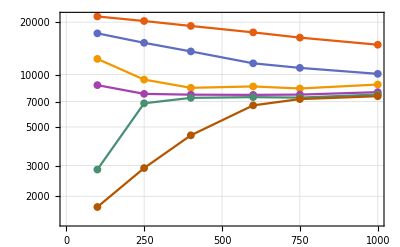

```mathematica
(*Tiempos de ejecución MH VS beta y diferentes deltas. Todo para N = un millón*)
ListLogPlot[timeData, PlotTheme->"Scientific", 
FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Tiempo de ejecución}\\,\\,[s]"}, Preamble->{"\\usepackage{newtxmath}"}], 
PlotLegends->LineLegend[MaTeX[deltas], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}]],
Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, FrameStyle->Black]
```

```mathematica
single
```

## Traslape con el singlete

```mathematica
singlete = (1/Sqrt[2]){0,1,-1,0};
singletRho = ketsToDensity[{singlete}][[1]];
```

```mathematica
overlap[rho_, psi_]:= QuantumDotProduct[psi, rho.psi]
```

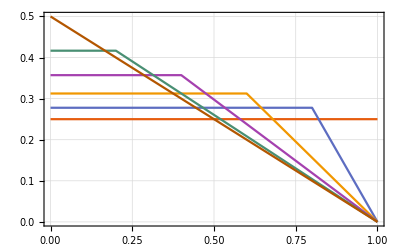

```mathematica
Plot[Evaluate@Table[overlap[ρaverageTwoQubitsbasiscomp[p, r], singlete], {p, swapPs}], {r,0, 1}, 
PlotTheme->"Scientific", PlotLegends->LineLegend[MaTeX[swapPs], LegendLabel->MaTeX["p", Preamble->{"\\usepackage{newtxmath}"}]],
FrameLabel->{MaTeX["r_z", Preamble->{"\\usepackage{newtxmath}"}], MaTeX["\\expval{\\mathcal{A}[\\varrho_t]}{\\Psi^-}", Preamble->{"\\usepackage{physics}"}]},
FrameStyle->Black, GridLines->Automatic]
```

```mathematica
Export["overlaps_2qubitAvg.pdf", %16]
```

overlaps_2qubitAvg.pdf

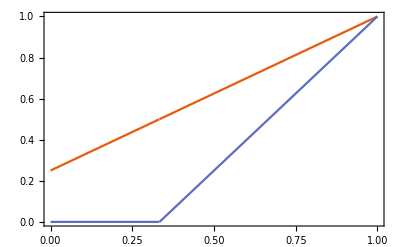

```mathematica
Plot[{overlap[α singletRho + (1-α)(IdentityMatrix[4]/4), singlete],
	  Concurrence[α singletRho + (1-α)(IdentityMatrix[4]/4)]}, {α, 0, 1}, 
	  PlotTheme->"Scientific", 
	  PlotLegends->Placed[MaTeX[{"\\expval{\\mathcal{A}[\\mathds{1}/2]}{\\Psi^-}", "C[\\mathcal{A}[\\mathds{1}/2]]"}, Preamble->{"\\usepackage{physics, dsfont}"}], {0.8,0.15}],
	  FrameLabel->MaTeX[{"\\alpha", "\\text{Valor}"}, Preamble->{"\\usepackage{newtxmath}"}],
	  FrameStyle->Black, GridLines->{{1/3}, {0.5}}, GridLinesStyle->Directive[Dashed, Red]]
```

```mathematica
Export["overlapAndConcurrence_R0avg.pdf", %42]
```

overlapAndConcurrence_R0avg.pdf

## Volumen

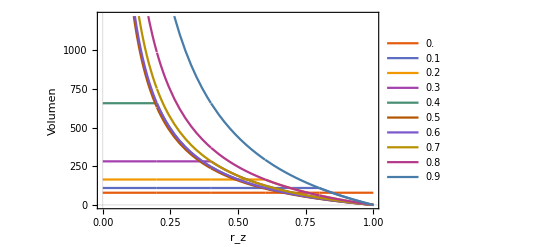

```mathematica
Plot[Evaluate@Table[volBipartiteSubSpaceTarget[p, r], {p, swapPs}], {r, 0, 1}, 
PlotLegends->swapPs, PlotTheme->"Scientific", FrameLabel->{"r_z", "Volumen"}]
```

```mathematica
(*con beta = 250*)
times = {{2267.756, 2346.957, 2235.642},
 {2025.71, 2062.962, 1952.112},
 {2040.3, 1996.822, 2002.237}};
```

```mathematica
Mean[Flatten[times]]/60
```

35.0565